```mathematica
SetDirectory[NotebookDirectory[]]
```

\\z-sv-pool01\J.Wienand\Desktop\cs-imaging\heatmap

```mathematica
U21 = Import["U21.csv","csv"];
U23 = Import["U23.csv","csv"];
U35 = Import["U35.csv","csv"];
U41 = Import["U41.csv","csv"];
U64 = Import["U64.csv","csv"];
U51 = Import["U51.csv","csv"];
U65 = Import["U65.csv","csv"];
U75 = Import["U75.csv","csv"];
U27 = Import["U27.csv","csv"];
U26 = Import["U26.csv","csv"];
U34 = Import["U34.csv","csv"];
D12 = Import["D12.csv","csv"];
D21 = Import["D21.csv","csv"];
D23 = Import["D23.csv","csv"];
D35 = Import["D35.csv","csv"];
D41 = Import["D41.csv","csv"];
D64 = Import["D64.csv","csv"];
D51 = Import["D51.csv","csv"];
D65 = Import["D65.csv","csv"];
D75 = Import["D75.csv","csv"];
D27 = Import["D27.csv","csv"];
D26 = Import["D26.csv","csv"];
D34 = Import["D34.csv","csv"];
D15 = Import["D15.csv","csv"];
PathA = Import["A.csv","csv"];
PathB =  Import["B.csv","csv"];
PathC = Import["C.csv","csv"];
PathD = Import["D.csv","csv"];
PathE = Import["E.csv","csv"];;
PathF =  Import["F.csv","csv"];
PathR =  Import["R.csv","csv"]; (*red imaging closed transition*)
```

```mathematica
nmax = Length[U21[[1]]] - 1
```

4

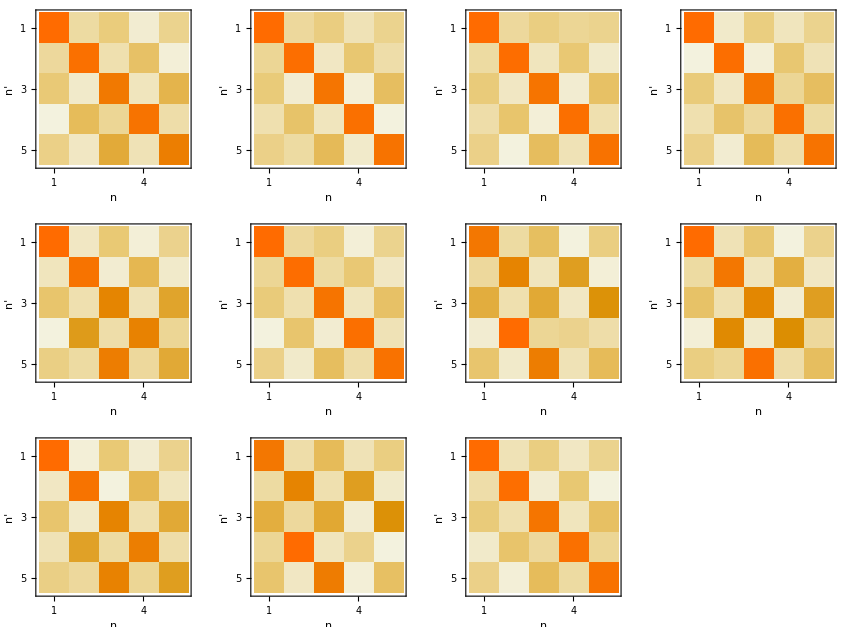

```mathematica
GraphicsGrid[{{MatrixPlot[U21,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 1"},{"n'",""}}],MatrixPlot[U23,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 3"},{"n'",""}}],MatrixPlot[U35,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 5"},{"n'",""}}],MatrixPlot[U41,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","4 -> 1"},{"n'",""}}]},{MatrixPlot[U64,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 4"},{"n'",""}}],MatrixPlot[U51,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","5 -> 1"},{"n'",""}}],MatrixPlot[U65,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 5"},{"n'",""}}],MatrixPlot[U75,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","7 -> 5"},{"n'",""}}]},{MatrixPlot[U27,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 7"},{"n'",""}}],MatrixPlot[U26,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 6"},{"n'",""}}],MatrixPlot[U34,FrameLabel -> {{"n","3 -> 4"},{"n'",""}}]}}]
```

```mathematica
Total[U41[[All,10]]]
```

1.02743182131628409

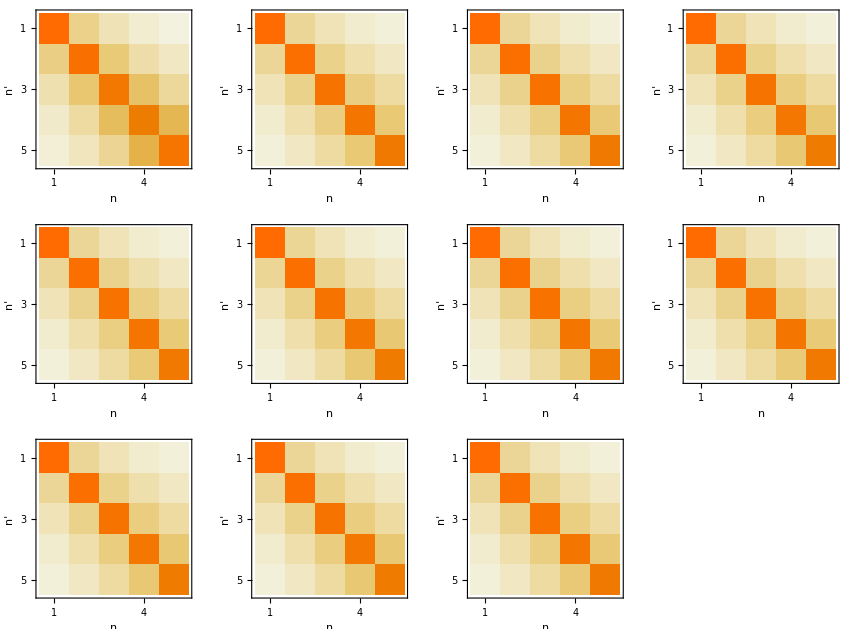

```mathematica
GraphicsGrid[{{MatrixPlot[D12,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","1 -> 2"},{"n'",""}}],MatrixPlot[D23,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 3"},{"n'",""}}],MatrixPlot[D35,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 5"},{"n'",""}}],MatrixPlot[D41,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","4 -> 1"},{"n'",""}}]},{MatrixPlot[D64,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 4"},{"n'",""}}],MatrixPlot[D51,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","5 -> 1"},{"n'",""}}],MatrixPlot[D65,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 5"},{"n'",""}}],MatrixPlot[D75,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","7 -> 5"},{"n'",""}}]},{MatrixPlot[D27,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 7"},{"n'",""}}],MatrixPlot[D26,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 6"},{"n'",""}}],MatrixPlot[D34,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 4"},{"n'",""}}]}}]
```

```mathematica
PathTot = 0.201004/(0.2001004+0.3678+0.25827)*PathA +0.3678/(0.2001004+0.3678+0.25827) PathB + 0.25827/(0.2001004+0.3678+0.25827) PathF;
PathTotE = 0.201004/(0.2001004+0.3678+0.25827+0.154494)*PathA +0.3678/(0.2001004+0.3678+0.25827+0.154494) PathB + 0.25827/(0.2001004+0.3678+0.25827+0.154494) PathF + 0.154494/(0.2001004+0.3678+0.25827 +0.154494)PathE;
(*+ +0.001969 PathC +0.016289PathD + 0.154494PathE ;*)
Paths ={PathA, PathB, PathC, PathD, PathE, PathF, PathTotE, PathTot, PathR};
```

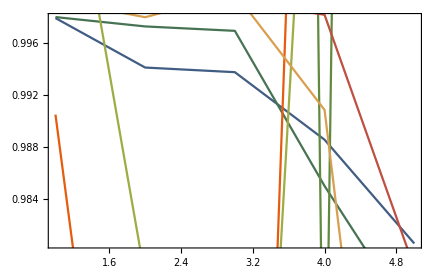

```mathematica
Show[{ListPlot[Table[Total[Table[Abs[PathA[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][1/8], Joined -> True, PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathB[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][2/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathC[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][3/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathD[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][4/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathE[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"]}[5/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathF[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"][6/8]},Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],
ListPlot[Table[Total[Table[Abs[PathR[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"][7/8]},Joined -> True,PlotTheme -> "Scientific",PlotRange-> All]
}]
```

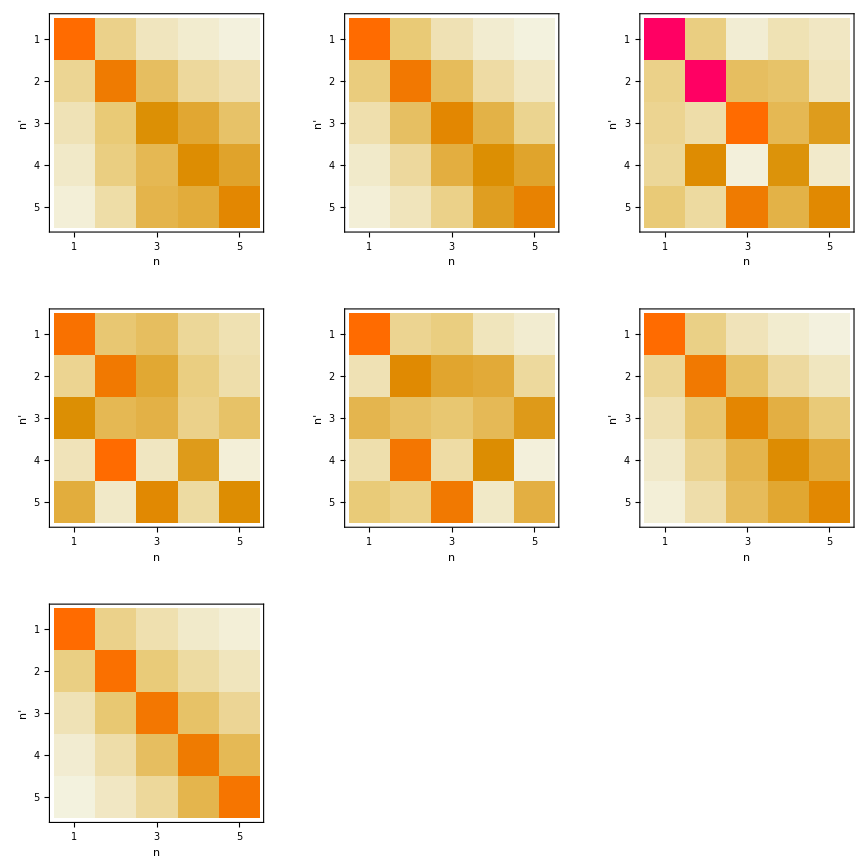

```mathematica
GraphicsGrid[{{MatrixPlot[PathA,FrameLabel -> {{"n","Path A: 2 -> 3 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],
MatrixPlot[PathB,FrameLabel -> {{"n","Path B: 2 -> 3 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],
MatrixPlot[PathC,FrameLabel -> {{"n","Path C: 2 -> 6 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}]
},
{MatrixPlot[PathD,FrameLabel -> {{"n","Path D: 2 -> 6 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}],
MatrixPlot[PathE,FrameLabel -> {{"n","Path E: 2 -> 7 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}],
MatrixPlot[PathF,FrameLabel -> {{"n","Path F: 2 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ]},{MatrixPlot[PathR,FrameLabel -> {{"n","Path Red Imaging: 1 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],None,None}}, FrameStyle-> Black]
```

```mathematica
Total[PathE[[2]]]
```

0.937979683676778045

```mathematica
tablePath[pa_]:=Table[Sum[Paths[[pa]][[r,All]][[ra]] ra,{ra,1,nmax+1}],{r,1,Length[Paths[[pa]][[1,All]]]}]
tablePath[6]
tablePath[1]
tablePath[2]
tablePath[5]
```

{1.15180816687955907,2.23902076966313416,3.2617789327748597,3.808247514448251,4.00643051377180326}

{1.18765147784587798,2.32550838367517138,3.36527911457058285,3.77781522439451392,4.10982654906818521}

{1.12297995873432753,2.15353890424503085,3.15769303003240706,3.93656574814251756,4.39361196537825862}

{1.61014240089889542,2.67946957674135401,2.89336353659271245,2.91665553883939573,3.15149756943942183}

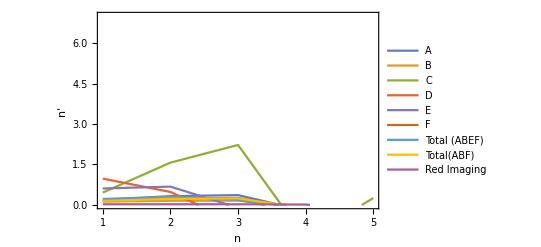

```mathematica
heatdata=Table[Table[Sum[Paths[[pa]][[r]][[ra]] ra,{ra,1,nmax+1}]-r,{r,1,Length[Paths[[pa]][[1,All]]]}],{pa,1,9}];
ListPlot[heatdata,PlotStyle -> ColorData["DarkRainbow"][pa/9],Joined -> True,FrameStyle -> Black, Frame -> True,PlotRange-> {{1,5},{0,7}}, FrameLabel->{"n", "n'"}, PlotLegends-> {"A","B","C","D","E","F","Total (ABEF)","Total(ABF)","Red Imaging"}]
```

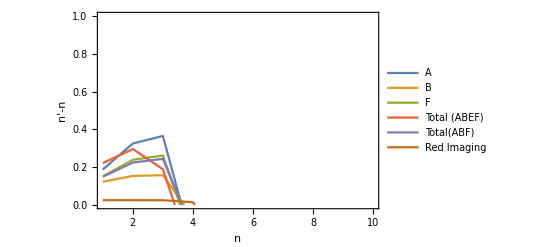

```mathematica
heatdata=Table[Table[Sum[Paths[[pa]][[r]][[ra]] ra,{ra,1,nmax+1}]-r,{r,1,Length[Paths[[pa]][[1,All]]]}],{pa,{1,2,6,7,8,9}}];
ListPlot[heatdata,PlotStyle -> ColorData["DarkRainbow"][pa/9],Joined -> True,FrameStyle -> Black, Frame -> True,PlotRange-> {{1,10},{0,1}}, FrameLabel->{"n", "n'-n"}, PlotLegends-> { "A","B","F","Total (ABEF)","Total(ABF)","Red Imaging"}]
```

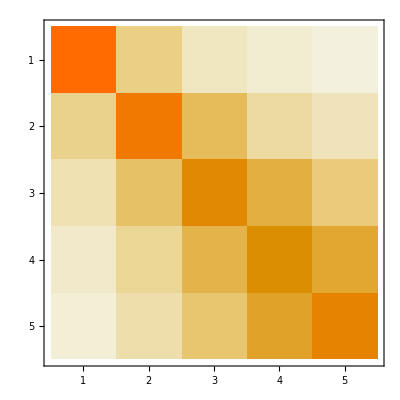

```mathematica
MatrixPlot[PathTot]
```

Multi-Experimente

```mathematica
intensities = Import["intensities.csv","csv"];
```

```mathematica
heatings = Import["heatings.csv", "csv"];
```

```mathematica
totheating = 0.201004/(0.2001004+0.3678+0.25827)*heatings[[All,1]]+0.3678/(0.2001004+0.3678+0.25827) heatings[[All,2]] + 0.25827/(0.2001004+0.3678+0.25827) heatings[[All,6]];
totheatingE = 0.201004/(0.2001004+0.3678+0.25827+0.154494)*heatings[[All,1]]+0.3678/(0.2001004+0.3678+0.25827+0.154494) heatings[[All,2]] + 0.25827/(0.2001004+0.3678+0.25827+0.154494) heatings[[All,6]] + 0.154494/(0.2001004+0.3678+0.25827 +0.154494)heatings[[All,5]];

heatingsext = Transpose[{heatings[[All,1]],heatings[[All,2]],heatings[[All,3]],heatings[[All,4]],heatings[[All,5]],heatings[[All,6]],heatings[[All,7]],totheating,totheatingE}];
```

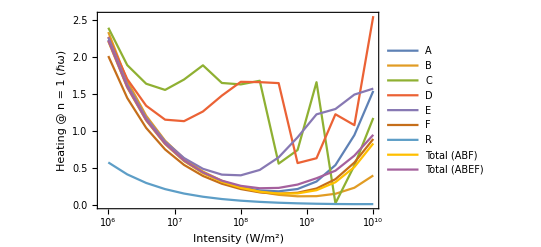

```mathematica
ListLogLinearPlot[Table[Thread[{Flatten[intensities], heatingsext[[All,in]]}],{in,1,9}], Joined -> True, PlotLegends-> {"A","B","C","D","E","F","R", "Total (ABF)", "Total (ABEF)"}, Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Heating @ n = 1 (ℏω)"}]
```

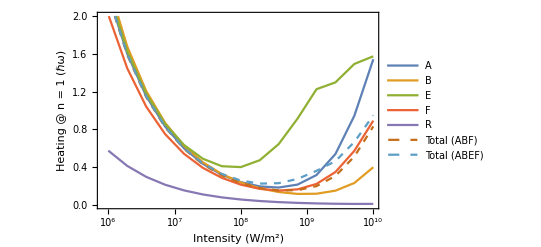

```mathematica
ListLogLinearPlot[Table[Thread[{Flatten[intensities], heatingsext[[All,in]]}],{in,{1,2,5,6,7,8,9}}], Joined -> True, PlotLegends-> {"A","B","E","F","R", "Total (ABF)", "Total (ABEF)"}, Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Heating @ n = 1 (ℏω)"}, PlotStyle ->{Normal,Normal,Normal,Normal,Normal,Dashed,Dashed}, Axes-> True, PlotRange -> {Automatic, {0, 2}}]
```

```mathematica
minima = FindMinimum[Interpolation[Transpose[{x,heatingsext}]][x],x]
```

Transpose::nmtx: The first two levels of {x,{{2.23336974666734456,2.33984936407508615,2.39820040821765934,2.27504932783591807,2.26760775679791493,2.01492414157389765,0.575224995436857123,2.21493,2.22323},«13»,{1.54271861922062348,0.399095038500593136,«6»,0.949017}}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{x,{{2.23336974666734456,2.33984936407508615,2.39820040821765934,2.27504932783591807,2.26760775679791493,2.01492414157389765,0.575224995436857123,2.21493,2.22323},«13»,{1.54271861922062348,«7»,0.949017}}}] does not contain a list of data and coordinates.

Transpose::nmtx: The first two levels of {x,{{2.23336974666734456,2.33984936407508615,2.39820040821765934,2.27504932783591807,2.26760775679791493,2.01492414157389765,0.575224995436857123,2.21493,2.22323},«13»,{1.54271861922062348,0.399095038500593136,«6»,0.949017}}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{x,{{2.23336974666734456,2.33984936407508615,2.39820040821765934,2.27504932783591807,2.26760775679791493,2.01492414157389765,0.575224995436857123,2.21493,2.22323},«13»,{1.54271861922062348,«7»,0.949017}}}] does not contain a list of data and coordinates.

Transpose::nmtx: The first two levels of {x,{{2.23337,2.33985,2.3982,2.27505,2.26761,2.01492,0.575225,2.21493,2.22323},«13»,{1.54272,0.399095,1.17731,2.55518,1.57438,0.892686,0.0111628,0.832073,0.949017}}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Interpolation::innd: First argument in Transpose[{x,{{2.23337,2.33985,2.3982,2.27505,2.26761,2.01492,0.575225,2.21493,2.22323},«13»,{1.54272,0.399095,1.17731,2.55518,1.57438,0.892686,0.0111628,0.832073,0.949017}}}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

FindMinimum::nrnum: The function value Interpolation[Transpose[{1.,{{2.233369746667345,2.339849364075086,2.398200408217659,2.275049327835918,2.267607756797915,2.014924141573898,0.5752249954368571,2.21493,2.22323},«13»,{1.542718619220623,0.3990950385005931,«6»,0.949017}}}]][1.] is not a real number at {x} = {1.}.

FindMinimum[Interpolation[Transpose[{x,heatingsext}]][x],x]